Analiza cen zemeljskega plina v Sloveniji

V  tej seminarski nalogi si bomo malo ogledali gibanje cen zemeljskega plina od leta 2012 do leta 2021.

## Pridobivanje podatkov

Podatke sem pridobil iz statističnega urada republike slovenije oziroma na kratko SiStat. Ogledamo si jih lahko na  spletni strani “https://pxweb.stat.si/SiStatData/pxweb/sl/Data/-/1817505S.px”. Podatke sem uredil tako da sem vzel vse standerdne porabe za gospodinske odjemalce, Enota je EUR/GJ in v ceno so ušteti vsi davki. Datoteko sem prenesel v obliki CSV(ločeno z vejico) z glavo(.csv).

Najprej bomo uvozili podatke kot je opisano zgoraj.

```mathematica
data=Import[NotebookDirectory[]<> "cene_urejena.csv", "Table", FieldSeparators -> ",", HeaderLines -> 2, CharacterEncoding->"WindowsEastEurope"]//Transpose//ResourceFunction["DatasetWithHeaders"]
```

Dataset[<>]

## Urejanje pridobljenih podatkov

Sedaj nastopi čiščenje in urejanje podatko za nadalno uporabo.

Za lažji pregled podatkov sem kar napisal funkcijo. Izgubili bomo prvi dve vrstici tabele saj enote in podatka kako je z davki za naprej ne potrebujemo.

Funkcija deluje tako za želeno skupino vpišemo število kot pravi legenda.

D1=1
D2=2
D3=3
Slovenija=4

Funkcija nam uredi podate po letih, kvartalih in po razredu porabe plina ki ga vpišemo v funkcijo.

```mathematica
pregled[D_]:=data //
Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]
```

```mathematica
pregled[3]
```

Dataset[<>]

## Analiza podatkov

### Povprečja glede na kvartale čez vsa leta

Funkcija deluje tako, da vanjo vnesemo podatke glede na porabo (D1,D2,D3,Slovenija), iz nje dobimo podatke kakšna je povprečna cena plina glede na razred porabe v letih med 2012 do 2021.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
povprečjaobdobja[D_]:=data //Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]//
Query[GroupBy[#obdobje&]/*Values,<|
"obdobje"-> Query[First,"obdobje"],
"opovprečje"->Query[Mean,3]
|>]
```

```mathematica
povprečjaobdobja[1]
```

Dataset[<>]

Funkcija nam nariše tortni diagram za povprečne cene plina glede na razred porabe.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Piechartpovprečjaobdobje[D_]:=PieChart[povprečjaobdobja[D]//Query[All,2],ChartLegends->{Q1,Q2,Q3,Q4}]
```

```mathematica
Piechartpovprečjaobdobje[1]
```

-Graphics-

Funkcija nam nariše graf kako se spreminja povprečna cena po kvartalih.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Grafpovprečjaobdobje[D_]:=ListLinePlot[povprečjaobdobja[D]//Query[All,2],
PlotLabel->"POVPREČNA CENA PO KVARTALIH", 
FrameLabel->{ "KVARTAL", "POVPREČNA CENA"}, 
Frame-> {{True, False}, {True, False}}
]
```

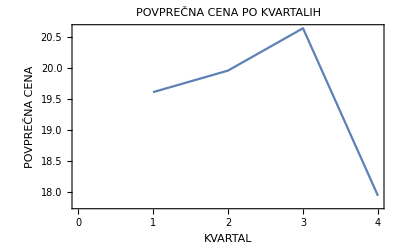

```mathematica
Grafpovprečjaobdobje[1]
```

### Leta(povprečne vrednosti)

Funkcija nam vrne tabelo, kjer izračunomo povprečno ceno plina glede na leto. V funkcijo vnesemo želeni razred porabe kot kaze legenda.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Povprečnaleto[D_]:=data //
Query[3;;, {1,1+D}] //Query[All, <| "leto" -> ToExpression[StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4]], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}] //
Query[GroupBy[#leto&]/*Values,<|
"leto"-> Query[First,"leto"],
"povprecje"->Query[Mean,3]
|>
]
```

```mathematica
Povprečnaleto[1]
```

Dataset[<>]

Funkcija nam zriše graf glede na povprečno letno ceno plina. V funkcijo vnsemo želeni razred porabe kot kaže legenda.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Grafpovprečnaleto[D_]:=ListLinePlot[Povprečnaleto[D]//Query[All,{1,2}],
PlotLabel->"povprečna leto", 
FrameLabel->{ "leto", "povprečna cena"}, 
Frame-> {{True, False}, {True, False}}
]
```

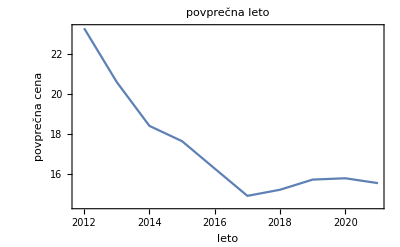

```mathematica
Grafpovprečnaleto[4]
```

### Natančneje po letih

Funkcija nam osnovne podatke z GrupBy-em uredi, da imamo tabelo ločeno po letih. Funkcija sprejme en parameter in sicer razred porabe.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Grupiranjepoletih[D_]:=GroupBy[data //
Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}] //Query[All,All],"leto"]
```

```mathematica
Grupiranjepoletih[4]
```

Dataset[<>]

Funkcija sprejme 2 parametra in sicer prvi je razred porabe ter drugi leto ki ga zapišemo v obliki “leto”. Funkcija nam vrne tabelo cen plina razdeljeno na kvartale za naš rezred porabe in leto.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Natančenpogled[D_,leto_]:=data //Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]//
GroupBy[#//Query[All,All],"leto"]&//
#[leto]&//
Query[All,{2,3}]
```

```mathematica
Natančenpogled[1,"2012"]
```

Dataset[<>]

Funkcija sprejem dva parametra razred porabe in leto ki nas zanima. Ter za te podatke zriše graf kjer imamo na eni osi ceno na drugi pa kvartale.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
Grafnatančna[D_,leto_]:=data //Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]//
GroupBy[#//Query[All,All],"leto"]&//
#[leto]&//
Query[All,3]//
ListLinePlot[
#, 
PlotLabel->" CENA PLINA"  leto , 
FrameLabel->{ "KVARTAL", "CENA"}, 
Frame-> {{True, False}, {True, False}}
]&
```

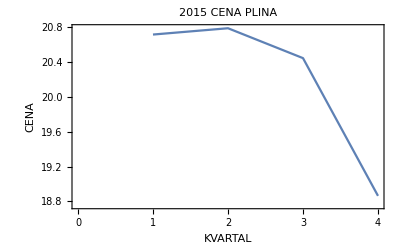

```mathematica
Grafnatančna[1,"2015"]
```